```mathematica
ClearAll["Global`*"]
```

```mathematica
(*test case 1*)
```

```mathematica
u[x_]:=Sin[2 π x/L]
Lu[x_]:=-(2 π /L)^2Sin[2 π x/L]
gradu[x_]:=2π /L Cos[2 π x/L]
```

```mathematica
L=1;
```

```mathematica
(*check for u*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/periodic/solution/nodal_values/u.csv"];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

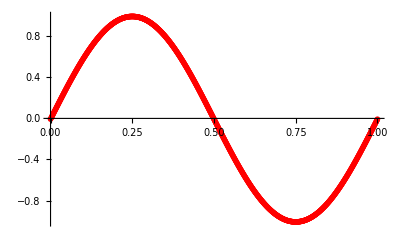

```mathematica
plotnum=ListPlot[t,PlotStyle->{Red,PointSize->0.01}]
```

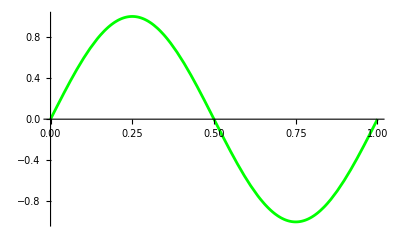

```mathematica
plotexact=Plot[u[x],{x,0,L},PlotRange->Full,PlotStyle->Green]
```

```mathematica
δ=Max[Table[Abs[t[[i,2]]-u[t[[i,1]]]],{i,1,Length[t]}]]
```

0.007481

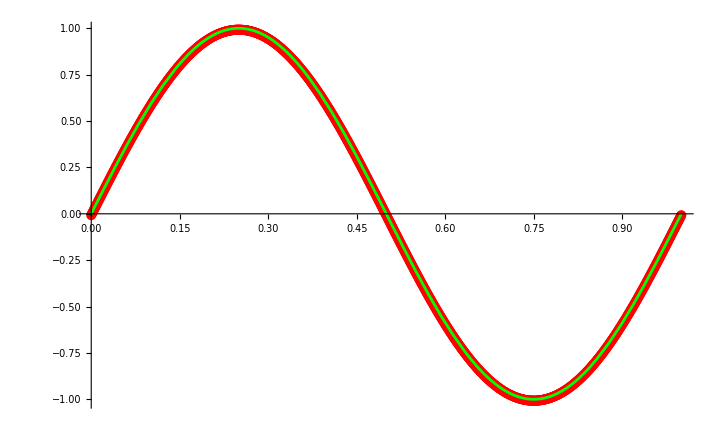

```mathematica
Show[plotnum,plotexact]
```